```mathematica
sumIntDigits[n_, b_]:=Total[IntegerDigits[n, b]]
```

```mathematica
sumIntDigits[17, 10]
```

8

```mathematica
sumIntDigits[10, 2]
```

2

```mathematica
expSumList[n_ ,b_, p_]:=Prepend[Accumulate[Exp[2.0*Pi*I*sumIntDigits[#, b]/p]&/@Range[n]], 0]
```

```mathematica
Range[4.23123]
```

{1,2,3,4}

```mathematica
expSumList[1000,10, 4];
```

```mathematica
expSumList[7, 2, 3]
```

{0,-0.5+0.866025 ⅈ,-1.+1.73205 ⅈ,-1.5+0.866025 ⅈ,-2.+1.73205 ⅈ,-2.5+0.866025 ⅈ,-3.+1.33227×10^-15 ⅈ,-2.+1.08734×10^-15 ⅈ}

```mathematica
visualizer[n_, b_, p_]:=ListLinePlot[ReIm /@ expSumList[n,b, p], PlotStyle->Thick]
```

```mathematica
chunkVisualizer[n1_, n2_, b_, p_, c_]:=ListLinePlot[ReIm /@ Take[expSumList[n2,b, p], {n1, n2+1}], PlotStyle->{Thick, c}]
```

```mathematica
pointVisualizer[n_, b_, p_]:=ListPlot[ReIm /@ expSumList[n,b, p], PlotStyle->{PointSize[Large], Red}]
```

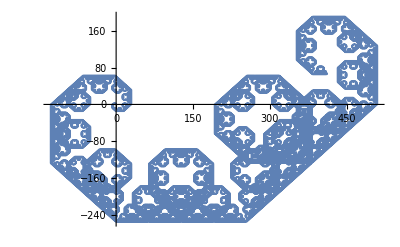

```mathematica
visualizer[100000, 2, 4]
```

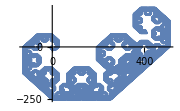

```mathematica
Show[%,ImageSize->Small]
```

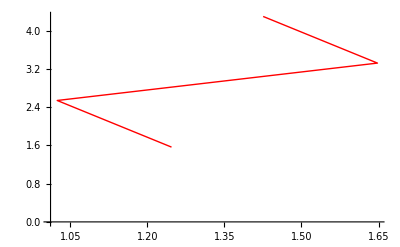

```mathematica
chunkVisualizer[3,5,2, 7, Red]
```

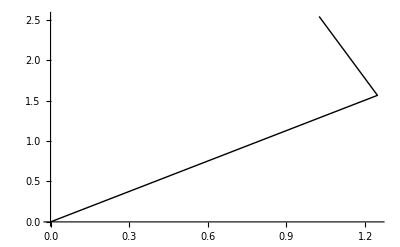

```mathematica
chunkVisualizer[1,3,2, 7, Black]
```

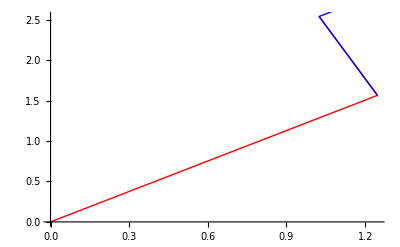

```mathematica
Show[chunkVisualizer[1,3,2, 7, Red], chunkVisualizer[3,5,2, 7, Blue]]
```

```mathematica
(* Table of some integer visualizations in base 10, varying by param p *)
```

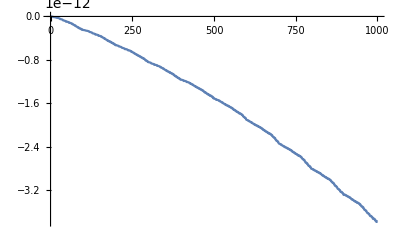
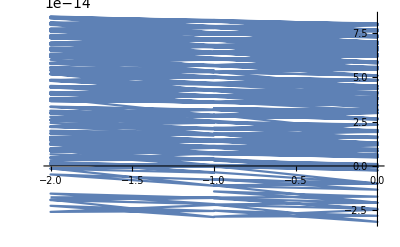
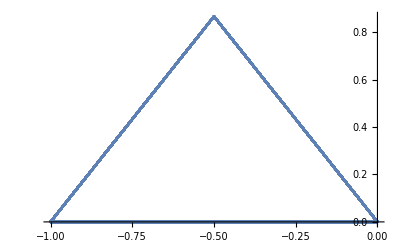
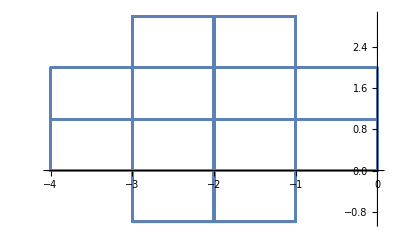
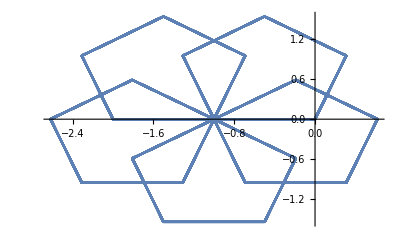
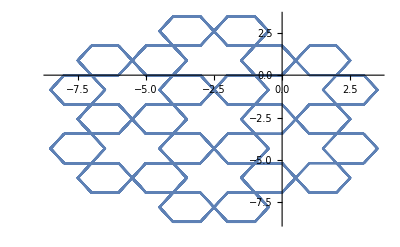
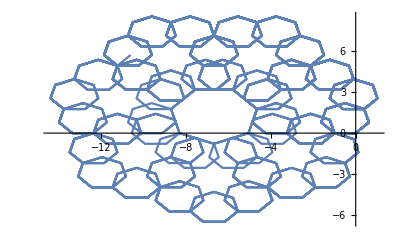
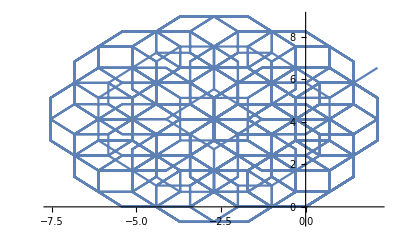
{{1,-Graphics-},{2,-Graphics-},{3,-Graphics-},{4,-Graphics-},{5,-Graphics-},{6,-Graphics-},{7,-Graphics-},{8,-Graphics-},{9,-Graphics-},{10,-Graphics-}}

```mathematica
Table[{k,ListLinePlot[(ReIm /@ expSumList[1000, 10, k])]}, {k, Range[10]}]
```

```mathematica
(* Table of some integer visualizations in base 10, varying by param n *)
```

```mathematica
Manipulate[list = ReIm /@ expSumList[10000, 2, 4];
maxRange = Max[Abs[list]];
ListLinePlot[Take[list,t],PlotRange->{{-maxRange, maxRange},{-maxRange, maxRange}}], {t, 1, 10000, 1}]
```

ListLinePlot::prng: Value of option PlotRange -> {{-Abs[expSumList[{10000,0},{2,0},{4,0}]],Abs[expSumList[{10000,0},{2,0},{4,0}]]},{-Abs[expSumList[{10000,0},{2,0},{4,0}]],Abs[expSumList[{10000,0},{2,0},{4,0}]]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

ListLinePlot::lpn: expSumList[{10000.,0.}] is not a list of numbers or pairs of numbers.

```mathematica
Manipulate[list = ReIm /@ expSumList[10000, 2, 1/Sqrt[3]];
partialList = Take[list, t];
maxRange = Max[Abs[partialList]]*1.1;
Graphics[Line[partialList], PlotRange->{{-maxRange, maxRange},{-maxRange, maxRange}}, Axes->True], {t, 2, 10000, 10}]
```

```mathematica
(* Table of some integer visualizations varying in base *)
```

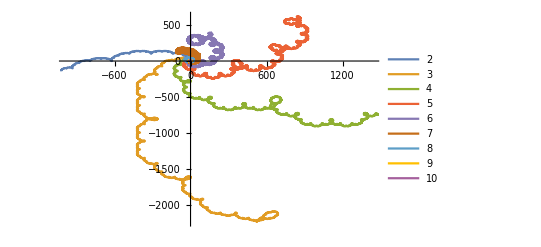

```mathematica
ListLinePlot[(ReIm /@ expSumList[10000, #, 10])& /@ Range[2,10], PlotLegends->Range[2,10]]
```

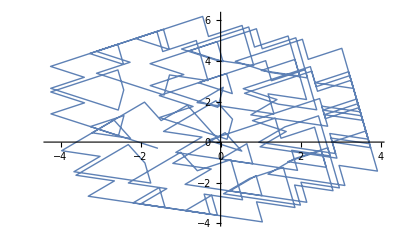

```mathematica
visualizer[250, 2, Pi]
```

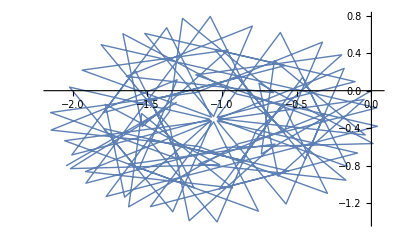

```mathematica
visualizer[100, 10, GoldenRatio]
```

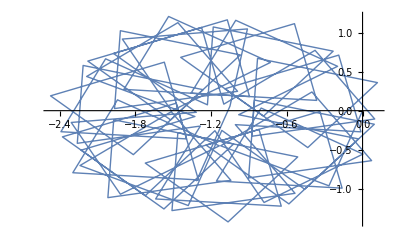

```mathematica
visualizer[100, 10, Sqrt[2]]
```

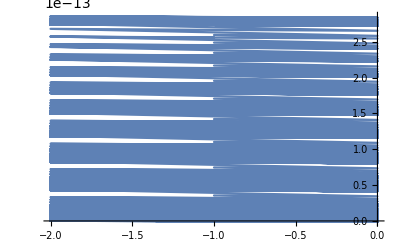
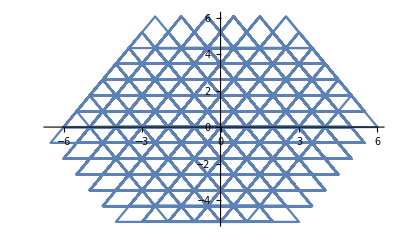
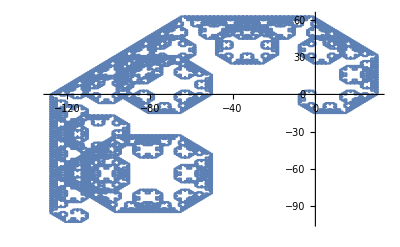
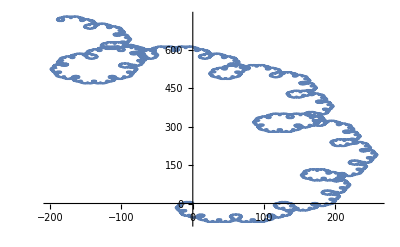
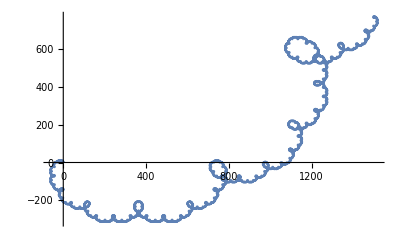
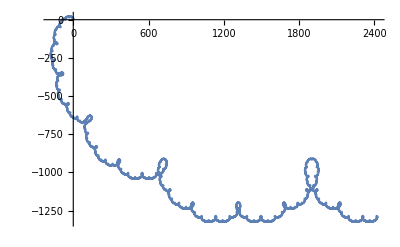
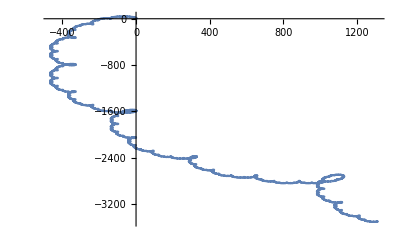
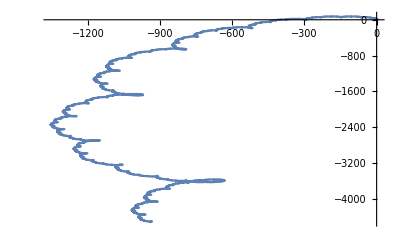
{{2,-Graphics-},{3,-Graphics-},{4,-Graphics-},{5,-Graphics-},{6,-Graphics-},{7,-Graphics-},{8,-Graphics-},{9,-Graphics-},{10,-Graphics-}}

```mathematica
(*Table of sumWalks for base 2*)
Sort[Table[{x, ListLinePlot[ReIm /@ expSumList[10000, 2, x]]}, {x, Range[2,10]}]]
```

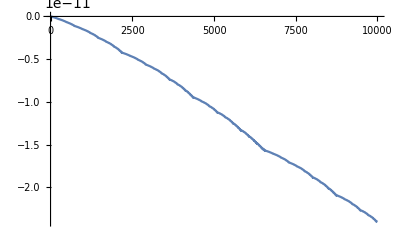
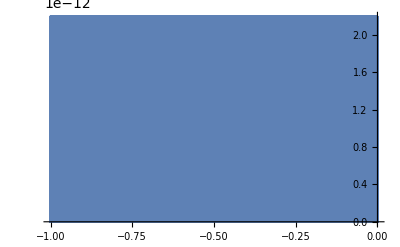
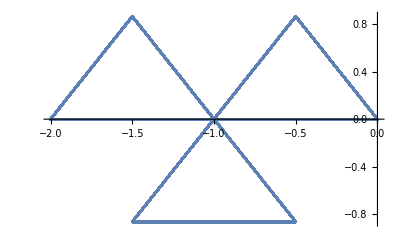
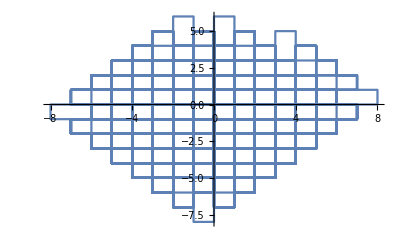
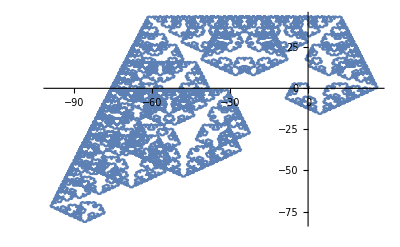
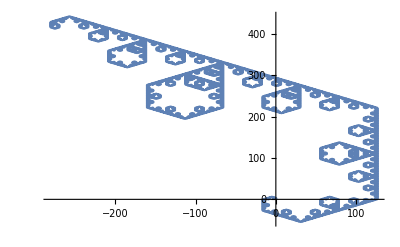
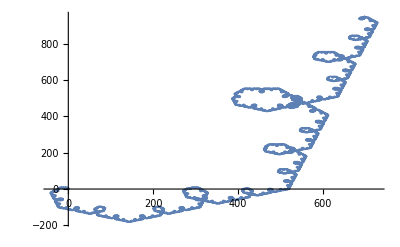
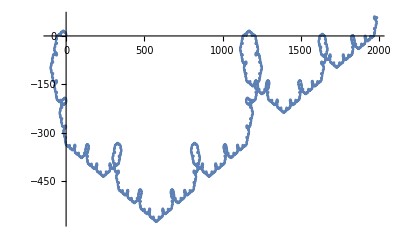
{{1,-Graphics-},{2,-Graphics-},{3,-Graphics-},{4,-Graphics-},{5,-Graphics-},{6,-Graphics-},{7,-Graphics-},{8,-Graphics-},{9,-Graphics-},{10,-Graphics-}}

```mathematica
(*Table of sumWalks for base 3*)
Sort[Table[{x, ListLinePlot[ReIm /@ expSumList[10000, 3, x]]}, {x, Range[10]}]]
```

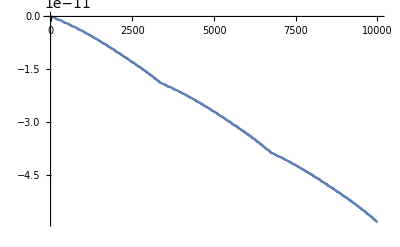
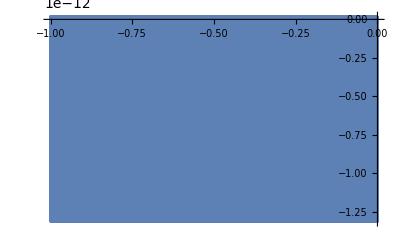
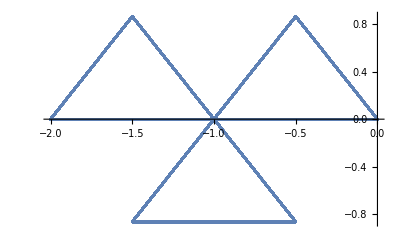
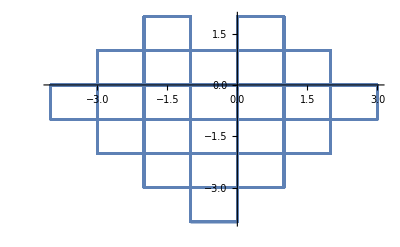
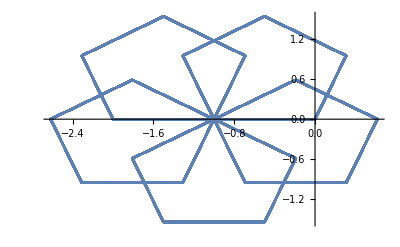
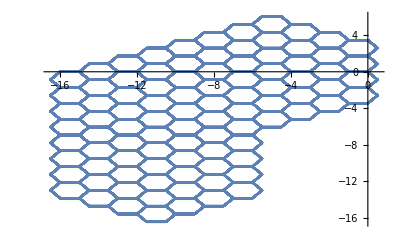
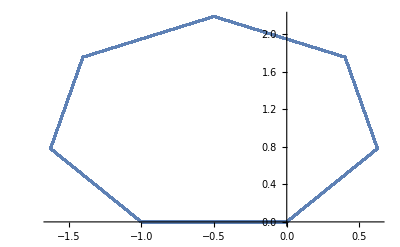
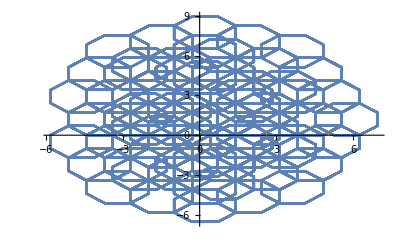
{{1,-Graphics-},{2,-Graphics-},{3,-Graphics-},{4,-Graphics-},{5,-Graphics-},{6,-Graphics-},{7,-Graphics-},{8,-Graphics-},{9,-Graphics-},{10,-Graphics-}}

```mathematica
(*Table of sumWalks for base 15*)
Sort[Table[{x, ListLinePlot[ReIm /@ expSumList[10000, 15, x]]}, {x, Range[10]}]]
```

```mathematica
Animate[list = ReIm  /@ expSumList[n, b, p];
ListLinePlot[list], {n, 1, 10000, 1}, {b, 2, 15, 1},{p, 2, 15, 1}, AnimationRunning->False]
```

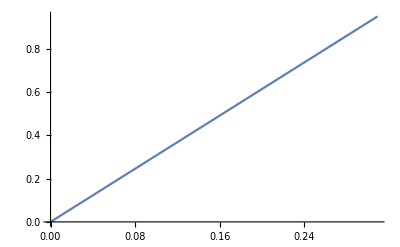
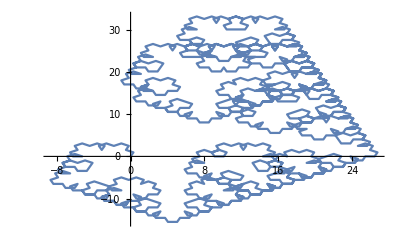
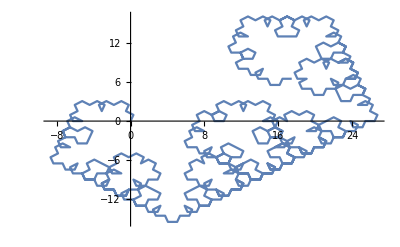
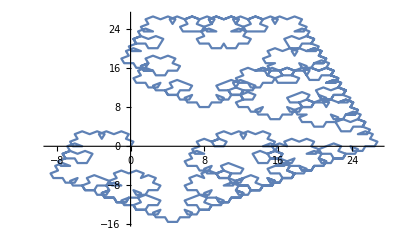
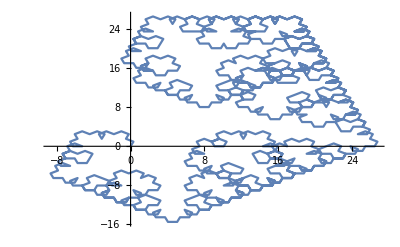
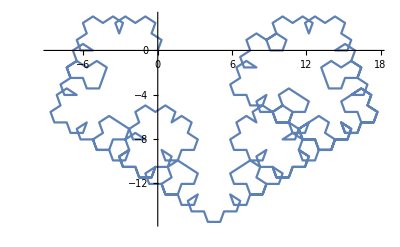
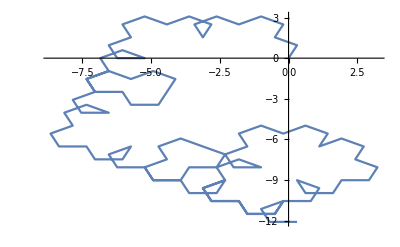
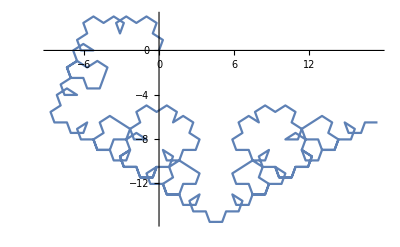
{{1,-Graphics-},{5,-Graphics-},{5,-Graphics-},{5,-Graphics-},{5,-Graphics-},{5,-Graphics-},{5,-Graphics-},{5,-Graphics-},{7,-Graphics-},{9,-Graphics-},{11,-Graphics-}}

```mathematica
Sort[Table[{Total[IntegerDigits[x, 3]], ListLinePlot[ReIm /@ expSumList[x, 3, 5]]}, {x, 1, 1001, 100}]]
```

```mathematica
termList=ReIm /@ expSumList[15, 2, 5]
```

{{0,0},{0.309017,0.951057},{0.618034,1.90211},{-0.190983,2.4899},{0.118034,3.44095},{-0.690983,4.02874},{-1.5,4.61653},{-2.30902,4.02874},{-2.,4.9798},{-2.80902,5.56758},{-3.61803,6.15537},{-4.42705,5.56758},{-5.23607,6.15537},{-6.04508,5.56758},{-6.8541,4.9798},{-6.54508,4.02874}}

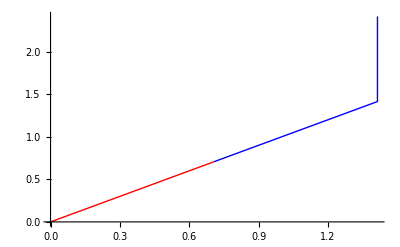
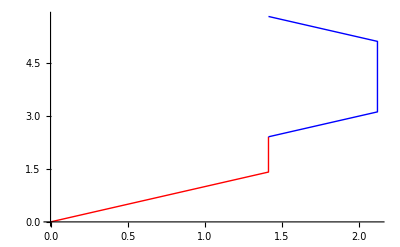
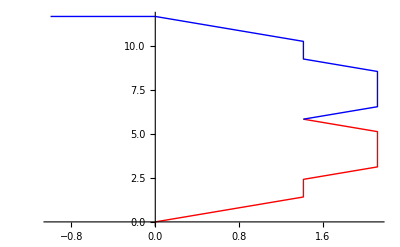
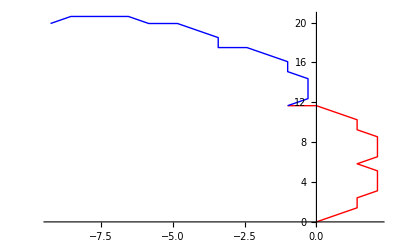
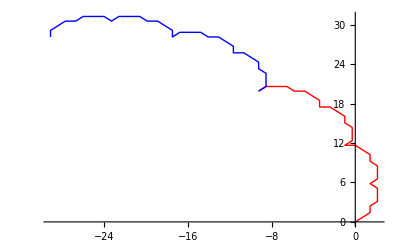
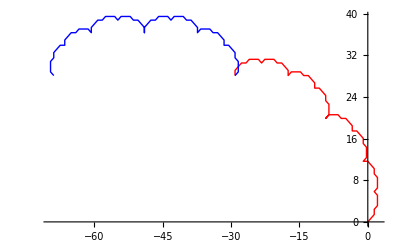
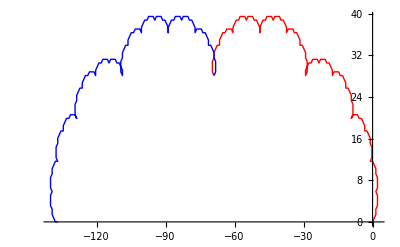
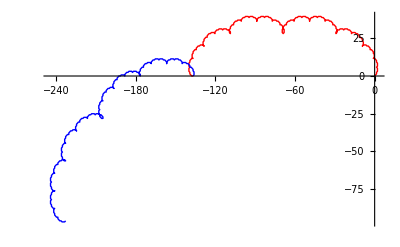

```mathematica
(* chunkVisualizer[1, 2^(k-1), 2, 10, Hue[k/10]], {k,1, 10, 1 } *)
Table[Show[{chunkVisualizer[1, 2^k - 1, 2, 8, Red], chunkVisualizer[2^k, 2^(k+1)-1, 2, 8, Blue]}, PlotRange->Full], {k,1, 15, 1}]
```

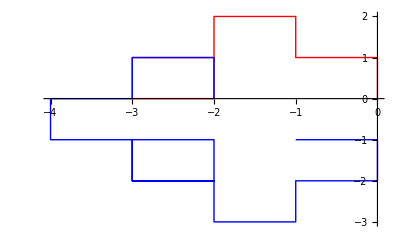

```mathematica
Show[{chunkVisualizer[1, 9, 3, 4, Red], chunkVisualizer[9, 26, 3, 4, Blue]}, PlotRange->Full]
```

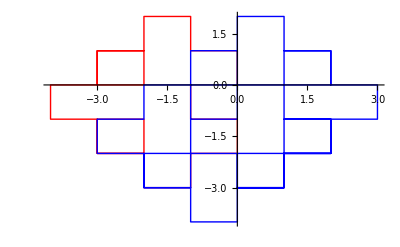

```mathematica
Show[{chunkVisualizer[1, 27, 3, 4, Red], chunkVisualizer[27, 81, 3, 4, Blue]}, PlotRange->Full]
```

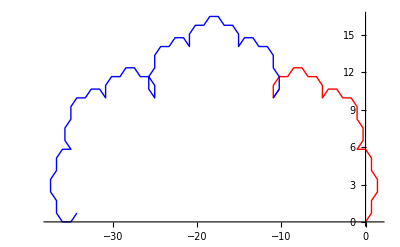

```mathematica
Show[{chunkVisualizer[1, 27, 3, 8, Red], chunkVisualizer[27, 81, 3, 8, Blue]}, PlotRange->Full]
```

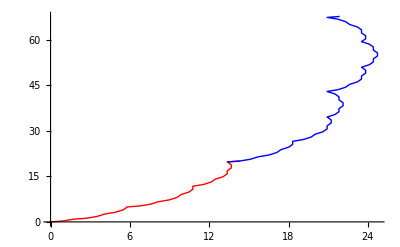

```mathematica
Show[{chunkVisualizer[1, 27, 3, 20, Red], chunkVisualizer[27, 81, 3, 20, Blue]}, PlotRange->Full]
```

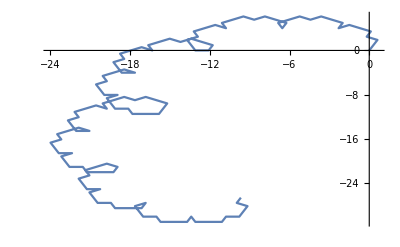
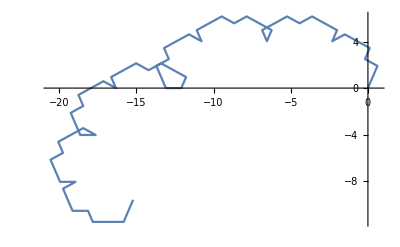
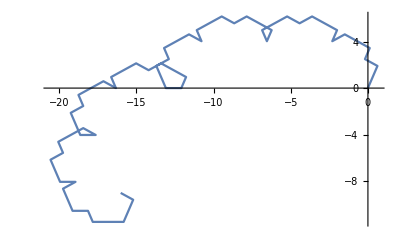
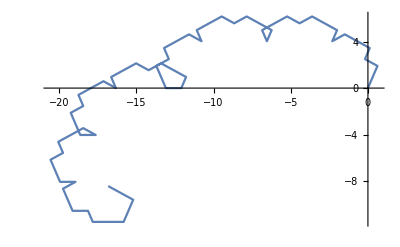
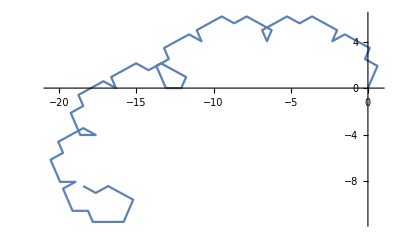
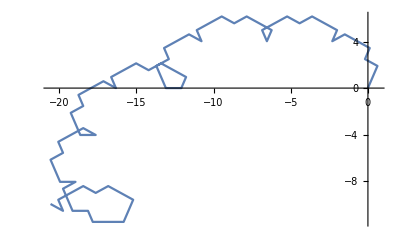
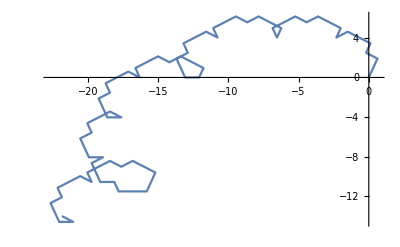
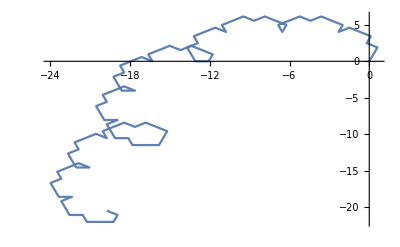
{{1,-Graphics-},{1,-Graphics-},{2,-Graphics-},{2,-Graphics-},{2,-Graphics-},{2,-Graphics-},{2,-Graphics-},{2,-Graphics-},{3,-Graphics-},{3,-Graphics-},{3,-Graphics-},{3,-Graphics-},{3,-Graphics-},{3,-Graphics-},{3,-Graphics-},{3,-Graphics-},{3,-Graphics-},{3,-Graphics-},{3,-Graphics-},{3,-Graphics-},{3,-Graphics-},{3,-Graphics-},{3,-Graphics-},{4,-Graphics-},{4,-Graphics-},{4,-Graphics-},{4,-Graphics-},{4,-Graphics-},{4,-Graphics-},{4,-Graphics-},{4,-Graphics-},{4,-Graphics-},{4,-Graphics-},{4,-Graphics-},{4,-Graphics-},{4,-Graphics-},{4,-Graphics-},{4,-Graphics-},{4,-Graphics-},{4,-Graphics-},{4,-Graphics-},{4,-Graphics-},{4,-Graphics-},{5,-Graphics-},{5,-Graphics-},{5,-Graphics-},{5,-Graphics-},{5,-Graphics-},{5,-Graphics-},{5,-Graphics-},{5,-Graphics-},{5,-Graphics-},{5,-Graphics-},{5,-Graphics-},{5,-Graphics-},{5,-Graphics-},{5,-Graphics-},{5,-Graphics-},{6,-Graphics-},{6,-Graphics-},{6,-Graphics-},{6,-Graphics-},{6,-Graphics-},{6,-Graphics-},{7,-Graphics-}}

```mathematica
Sort[Table[{Total[IntegerDigits[x, 2]], ListLinePlot[ReIm /@ expSumList[x, 2, 5]]}, {x, 64, 128, 1}]]
```

```mathematica
expSumList[5, 2, 7]
```

{0,0.62349+0.781831 ⅈ,1.24698+1.56366 ⅈ,1.02446+2.53859 ⅈ,1.64795+3.32042 ⅈ,1.42543+4.29535 ⅈ}

```mathematica
arrowVisualizer[n_, b_, p_]:=Graphics[
{Blue,
Thickness[0.0075],
Arrowheads[0.1], 
Arrow[ReIm /@ expSumList[#,b, p]]&/@ Range[n]
}, 
AspectRatio->1
]
```

```mathematica
arrowVisualizer[5,2,7]
```

-Graphics-

```mathematica
arrowAxesVisualizer[n_, b_, p_]:=Graphics[
{Blue,
Thickness[0.0075],
Arrowheads[0.1], 
Arrow[ReIm /@ expSumList[#,b, p]]&/@ Range[n]
}, 
AspectRatio->1,
Axes->True
]
```

```mathematica
arrowAxesVisualizer[5,2,7]
```

-Graphics-

Thread::tdlen: Objects of unequal length in IntegerDigits[{1},{2,0}] cannot be combined.

Power::infy: Infinite expression 1/0 encountered.

Thread::tdlen: Objects of unequal length in IntegerDigits[{},{2,0}] cannot be combined.

Power::infy: Infinite expression 1/0 encountered.

IntegerDigits::ibase: Base 0 is not an integer greater than 1.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Thread::tdlen: Objects of unequal length in {1+IntegerDigits[2,0]} {1/7,ComplexInfinity} cannot be combined.

General::stop: Further output of Thread::tdlen will be suppressed during this calculation.

-Graphics-

```mathematica
Show[{visualizer[100,10,Pi]}, LabelStyle->Large, Axes->False]
```

-Graphics-

```mathematica
Show[{pointVisualizer[50, 7, 6], visualizer[50,7,6]}, LabelStyle->Large]
```

-Graphics-

```mathematica
(*Cases where b = p*)
Table[Show[{chunkVisualizer[1, 2^k - 1, 4, 4, Red], chunkVisualizer[2^k, 2^(k+1)-1, 4, 4, Blue]}, PlotRange->Full], {k,1, 8, 1}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[Show[{chunkVisualizer[1, 2^k - 1, 3, 3, Red], chunkVisualizer[2^k, 2^(k+1)-1, 3, 3, Blue]}, PlotRange->Full], {k,1, 8, 1}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[Show[{chunkVisualizer[1, 2^k - 1, 5, 5, Red], chunkVisualizer[2^k, 2^(k+1)-1, 5, 5, Blue]}, PlotRange->Full], {k,1, 8, 1}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[Show[{chunkVisualizer[1, 2^k - 1, 6, 6, Red], chunkVisualizer[2^k, 2^(k+1)-1, 6, 6, Blue]}, PlotRange->Full], {k,1, 8, 1}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
(*Cases where b = 1 mod p*)
Table[Show[{chunkVisualizer[1, 2^k - 1, 4, 3, Red], chunkVisualizer[2^k, 2^(k+1)-1, 4, 3, Blue]}, PlotRange->Full], {k,1, 8, 1}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[Show[{chunkVisualizer[1, 2^k - 1, 5, 4, Red], chunkVisualizer[2^k, 2^(k+1)-1, 5, 4, Blue]}, PlotRange->Full], {k,1, 8, 1}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[Show[{chunkVisualizer[1, 2^k - 1, 6, 5, Red], chunkVisualizer[2^k, 2^(k+1)-1, 6, 5, Blue]}, PlotRange->Full], {k,1, 8, 1}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[Show[{chunkVisualizer[1, 2^k - 1, 7, 6, Red], chunkVisualizer[2^k, 2^(k+1)-1, 7, 6, Blue]}, PlotRange->Full], {k,1, 8, 1}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
(*Table of all the b = p cases up to 10*)
Table[{n, Show[{chunkVisualizer[1, 2^(k)-1, n, n, Blue]}, PlotRange->Full]}, {n,5, 25, 5}, {k, 10, 15, 1}]
```

{{{5,-Graphics-},{5,-Graphics-},{5,-Graphics-},{5,-Graphics-},{5,-Graphics-},{5,-Graphics-}},{{10,-Graphics-},{10,-Graphics-},{10,-Graphics-},{10,-Graphics-},{10,-Graphics-},{10,-Graphics-}},{{15,-Graphics-},{15,-Graphics-},{15,-Graphics-},{15,-Graphics-},{15,-Graphics-},{15,-Graphics-}},{{20,-Graphics-},{20,-Graphics-},{20,-Graphics-},{20,-Graphics-},{20,-Graphics-},{20,-Graphics-}},{{25,-Graphics-},{25,-Graphics-},{25,-Graphics-},{25,-Graphics-},{25,-Graphics-},{25,-Graphics-}}}

```mathematica
(*Irrational p values*)
Table[Show[{chunkVisualizer[1, 2^(8), n, Pi, Blue]}, PlotRange->Full], {n,{2, 3, 9, 10}}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[Show[{chunkVisualizer[1, 2^(8+1)-1, n, GoldenRatio, Blue]}, PlotRange->Full], {n,{2, 3, 9, 10}}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[Show[{chunkVisualizer[1, 2^(8+1)-1, n, EulerGamma, Blue]}, PlotRange->Full], {n,{2, 3, 9, 10}}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[Show[{chunkVisualizer[1, 2^(8+1)-1, n, Sqrt[2], Blue]}, PlotRange->Full], {n,{2, 3, 9, 10}}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
(*Koch Curve graphing*)
twistExpSumList[n_, b_, p_, q_] := Prepend[Accumulate[(Exp[2.0*Pi*I*(sumIntDigits[#, b]/p + (#/q))]&/@Range[n])], 0]
twistVisualizer[n_, b_, p_, q_]:=ListLinePlot[ReIm /@ twistExpSumList[n,b, p, q], PlotStyle->Thick]
```

```mathematica
twistVisualizer[1000, 2, 2, 3]
```

-Graphics-

```mathematica
Animate[list = ReIm /@ expSumList[1000, 10, 4*Pi];
partialList = Take[list, t];
maxRange = Max[Abs[partialList]]*1.1;
Graphics[
{Orange,
Line[partialList]}, 
PlotRange->{{-maxRange, maxRange},
{-maxRange, maxRange}}, 
Axes->False,
  Background->Black], 
{t, 2, 1000, 10}]
```

```mathematica
Animate[list = ReIm /@ expSumList[1000, 2, Sqrt[2]];
partialList = Take[list, t];
maxRange = Max[Abs[partialList]]*1.1;
Graphics[
{Orange,
Line[partialList]}, 
PlotRange->{{-maxRange, maxRange},
{-maxRange, maxRange}}, 
Axes->False,
  Background->Black],{t, 2, 1000, 10}]
```

```mathematica
(*Proving if b = 1 mod p, S_b(n) = n mod p*)
{Total[IntegerDigits[#, 6]], Mod[Total[IntegerDigits[#, 6]], 5]}& /@ Range[10]
```

{{1,1},{2,2},{3,3},{4,4},{5,0},{1,1},{2,2},{3,3},{4,4},{5,0}}

```mathematica
{Total[IntegerDigits[#, 8]], Mod[Total[IntegerDigits[#, 8]], 7]}& /@ Range[10]
```

{{1,1},{2,2},{3,3},{4,4},{5,5},{6,6},{7,0},{1,1},{2,2},{3,3}}

```mathematica
ReIm /@ Chop[expSumList[15, 6,5]]
```

{{0,0},{0.309017,0.951057},{-0.5,1.53884},{-1.30902,0.951057},{-1.,0},{0,0},{0.309017,0.951057},{-0.5,1.53884},{-1.30902,0.951057},{-1.,0},{0,0},{0.309017,0.951057},{-0.5,1.53884},{-1.30902,0.951057},{-1.,0},{0,0}}

```mathematica
(* We can see how these points just repeat in both cases, making just one p gon *)
ReIm /@ Chop[expSumList[15, 7,6]]
```

{{0,0},{0.5,0.866025},{0.,1.73205},{-1.,1.73205},{-1.5,0.866025},{-1.,0},{0,0},{0.5,0.866025},{0.,1.73205},{-1.,1.73205},{-1.5,0.866025},{-1.,0},{0,0},{0.5,0.866025},{0.,1.73205},{-1.,1.73205}}

```mathematica
visualizer[1000, 7, 2*Sqrt[6]]
```

-Graphics-

```mathematica
visualizer[500, 5, 8*Pi/3]
```

-Graphics-

```mathematica
(* 500-step visualizations varying by base *)
Table[visualizer[500, n, 8*Pi/3], {n, 3, 15, 1}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
8*Pi/3.
```

8.37758

```mathematica
{visualizer[500, 8, 8], visualizer[500, 8, 8*Pi/3]}
```

{-Graphics-,-Graphics-}

```mathematica
(*Varying first irrational graph by multiples of Sqrt 6*)
```

```mathematica
Table[visualizer[1000, 7, n*Sqrt[6]], {n, 1, 10, 1}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[visualizer[1000, n, 2*Sqrt[6]], {n, 3, 15, 1}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
2.*Sqrt[6]
```

4.89898

```mathematica
(* b is approximately close to p*)
{visualizer[1000,5,5],visualizer[1000, 5, 2*Sqrt[6]]}
```

{-Graphics-,-Graphics-}

```mathematica
(* b is approximately close to 1 mod p *)
{visualizer[1000,6,5],visualizer[1000, 6, 2*Sqrt[6]]}
```

{-Graphics-,-Graphics-}

```mathematica
visualizer[3000, 30, Pi]
```

-Graphics-

```mathematica
Table[visualizer[k*1000, n*10, Pi], {n, 1, 7,1}, {k,1,5, 1}]
```

{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

```mathematica
Table[visualizer[k*1000, n*10, n*Pi], {n, 1, 7,1}, {k,1,5, 1}]
```

{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

```mathematica
visualizer[1000, 40, 4*Pi]
```

-Graphics-

```mathematica
visualizer[1000, 20, 20]
```

-Graphics-

```mathematica
visualizer[3000, 70, Pi]
```

-Graphics-

```mathematica
visualizer[3000, 28, 20]
```

-Graphics-

```mathematica
visualizer[750, 28, 20]
```

-Graphics-

```mathematica
Table[visualizer[2^k, 3, 2*Sqrt[6]], {k, 5, 17}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Animate[visualizer[2^k, 3, 2*Sqrt[6]], {k, 5, 13}]
```

```mathematica
kmax = 13;
Manipulate[list = ReIm /@ expSumList[2^kmax, b, 2*Sqrt[6]];
maxRange = Max[Abs[list]];
ListLinePlot[Take[list,Floor[2^k]],PlotRange->{{-maxRange, maxRange},{-maxRange, maxRange}}], {k, 5, kmax,0.1, Animator, AnimationRate->1, AnimationRunning->True}, {b,2,10, 1, SetterBar}]
```

Take::take: Cannot take positions 1 through 32 in expSumList[{Re[2^kmax],Im[2^kmax]},{2,0},{2 √6,0}].

Take::take: Cannot take positions 1 through 32 in expSumList[{Re[2.^kmax],Im[2.^kmax]},{2.,0},{4.898979485566356,0}].

Take::take: Cannot take positions 1 through 32 in expSumList[{Re[2.^kmax],Im[2.^kmax]},{2.,0.},{4.89898,0.}].

General::stop: Further output of Take::take will be suppressed during this calculation.

ListLinePlot::prng: Value of option PlotRange -> {{-Abs[expSumList[{Re[Power[«2»]],Im[Power[«2»]]},{2,0},{2 Power[«2»],0}]],Abs[expSumList[{Re[2^kmax],Im[2^kmax]},{2,0},{2 √6,0}]]},{-Abs[expSumList[{Re[Power[«2»]],Im[Power[«2»]]},{2,0},{2 Power[«2»],0}]],Abs[expSumList[{Re[2^kmax],Im[2^kmax]},{2,0},{2 √6,0}]]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

Take::normal: Nonatomic expression expected at position 1 in Take[False,False].

ListLinePlot::lpn: Take[expSumList[{Re[2.^kmax],Im[2.^kmax]},{2.,0.},{4.89898,0.}],32] is not a list of numbers or pairs of numbers.

```mathematica
Table[visualizer[5000, 5, n*Sqrt[6]], {n, 1, 10}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
visualizer[5000, 5, 2*Sqrt[6]]
```

-Graphics-

```mathematica
visualizer[1000, 5, 5*Pi]
```

-Graphics-

```mathematica
Table[visualizer[2^k, 5, 2*Sqrt[6]], {k, 5, 15}] (* These patterns are kinda similar *)
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Manipulate[list = ReIm /@ expSumList[2^k, 5, 2*Sqrt[6]];
maxRange = Max[Abs[list]];
ListLinePlot[Take[list,Floor[2^k]],PlotRange->{{-maxRange, maxRange},{-maxRange, maxRange}}], {k, 5, 15,0.1, Animator, AnimationRate->1, AnimationRunning->True}]
```

Take::take: Cannot take positions 1 through 1024 in expSumList[{1024.,0},{5,0},{2 √6,0}].

Take::take: Cannot take positions 1 through 1024 in expSumList[{1024.,0},{5.,0},{4.898979485566356,0}].

Take::take: Cannot take positions 1 through 1024 in expSumList[{1024.,0.},{5.,0.},{4.89898,0.}].

General::stop: Further output of Take::take will be suppressed during this calculation.

ListLinePlot::prng: Value of option PlotRange -> {{-Abs[expSumList[{1024.,0},{5,0},{2 Power[«2»],0}]],Abs[expSumList[{1024.,0},{5,0},{2 √6,0}]]},{-Abs[expSumList[{1024.,0},{5,0},{2 Power[«2»],0}]],Abs[expSumList[{1024.,0},{5,0},{2 √6,0}]]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

Take::normal: Nonatomic expression expected at position 1 in Take[False,False].

ListLinePlot::lpn: Take[expSumList[{1024.,0.},{5.,0.},{4.89898,0.}],1024] is not a list of numbers or pairs of numbers.

Take::take: Cannot take positions 1 through 1024 in expSumList[{1024.,0},{5,0},{2 √6,0}].

Take::take: Cannot take positions 1 through 1024 in expSumList[{1024.,0},{5.,0},{4.898979485566356,0}].

Take::take: Cannot take positions 1 through 1024 in expSumList[{1024.,0.},{5.,0.},{4.89898,0.}].

General::stop: Further output of Take::take will be suppressed during this calculation.

ListLinePlot::prng: Value of option PlotRange -> {{-Abs[expSumList[{1024.,0},{5,0},{2 Power[«2»],0}]],Abs[expSumList[{1024.,0},{5,0},{2 √6,0}]]},{-Abs[expSumList[{1024.,0},{5,0},{2 Power[«2»],0}]],Abs[expSumList[{1024.,0},{5,0},{2 √6,0}]]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

Take::normal: Nonatomic expression expected at position 1 in Take[False,False].

ListLinePlot::lpn: Take[expSumList[{1024.,0.},{5.,0.},{4.89898,0.}],1024] is not a list of numbers or pairs of numbers.

```mathematica
{visualizer[1000,5,5],visualizer[1000, 5, 2*Sqrt[6]]}
```

{-Graphics-,-Graphics-}

```mathematica
2. * Sqrt[6]
```

4.89898

```mathematica
(* Let's look at the point where things get really clouded up *)
Table[visualizer[2^k, 5, 2*Sqrt[6]], {k, 15, 20}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
cf[val_,n_] := ContinuedFraction[val, n]
```

```mathematica
Last[N[Convergents[cf[2*Sqrt[6], 50]]]]
```

4.89898

```mathematica
Convergents[cf[2*Sqrt[6], 50]]
```

{4,5,44/9,49/10,436/89,485/99,4316/881,4801/980,42724/8721,47525/9701,422924/86329,470449/96030,4186516/854569,4656965/950599,41442236/8459361,46099201/9409960,410235844/83739041,456335045/93149001,4060916204/828931049,4517251249/922080050,40198926196/8205571449,44716177445/9127651499,397928345756/81226783441,442644523201/90354434940,3939084531364/804062262961,4381729054565/894416697901,38992916967884/7959395846169,43374646022449/8853812544070,385990085147476/78789896198729,429364731169925/87643708742799,3820907934506876/779939566141121,4250272665676801/867583274883920,37823089259921284/7720605765212481,42073361925598085/8588189040096401,374409984664705964/76426118085983689,416483346590304049/85014307126080090,3706276757387138356/756540575094624409,4122760103977442405/841554882220704499,36688357589206677596/7488979632860260401,40811117693184120001/8330534515080964900,363177299134679637604/74133255753507979601,403988416827863757605/82463790268588944501,3595084633757589698444/733843577902219535609,3999073050585453456049/816307368170808480110,35587669038441217346836/7264302523268687376489,39586742089026670802885/8080609891439495856599,352281605750654583769916/71909181654784654229281,391868347839681254572801/79989791546224150085880,3487228388468104620352324/711827514024577854916321,3879096736307785874925125/791817305570802005002201}

```mathematica
Convergents[cf[Sqrt[2], 50]]
```

{1,3/2,7/5,17/12,41/29,99/70,239/169,577/408,1393/985,3363/2378,8119/5741,19601/13860,47321/33461,114243/80782,275807/195025,665857/470832,1607521/1136689,3880899/2744210,9369319/6625109,22619537/15994428,54608393/38613965,131836323/93222358,318281039/225058681,768398401/543339720,1855077841/1311738121,4478554083/3166815962,10812186007/7645370045,26102926097/18457556052,63018038201/44560482149,152139002499/107578520350,367296043199/259717522849,886731088897/627013566048,2140758220993/1513744654945,5168247530883/3654502875938,12477253282759/8822750406821,30122754096401/21300003689580,72722761475561/51422757785981,175568277047523/124145519261542,423859315570607/299713796309065,1023286908188737/723573111879672,2470433131948081/1746860020068409,5964153172084899/4217293152016490,14398739476117879/10181446324101389,34761632124320657/24580185800219268,83922003724759193/59341817924539925,202605639573839043/143263821649299118,489133282872437279/345869461223138161,1180872205318713601/835002744095575440,2850877693509864481/2015874949414289041,6882627592338442563/4866752642924153522}

```mathematica
(* Taking previous comparison example and check it with new convergent value *)
```

```mathematica
{visualizer[1000,5,4.89898],visualizer[1000, 5, 2*Sqrt[6]]}
```

{-Graphics-,-Graphics-}

```mathematica
{visualizer[1000,5,44/9],visualizer[1000, 5, 2*Sqrt[6]]}
```

{-Graphics-,-Graphics-}

```mathematica
{visualizer[1000,5,49/10],visualizer[1000, 5, 2*Sqrt[6]]}
```

{-Graphics-,-Graphics-}

```mathematica
(* Now let's vary p and b *)
Manipulate[list = ReIm /@ expSumList[2^k, b, n*Sqrt[6]];
maxRange = Max[Abs[list]];
ListLinePlot[Take[list,Floor[2^k]],PlotRange->{{-maxRange, maxRange},{-maxRange, maxRange}}], {k, 5, 15,0.1, Animator, AnimationRate->1, AnimationRunning->True}, {b, 3, 10, 1, SetterBar}, {{n,1,"Factor of Sqrt[6]"}, 1, 5, 1, SetterBar}]
```

```mathematica
(* Finding general "tolerance" of p through which a clear rational-like pattern can form *)
Table[{k,visualizer[10000, 5, k]}, {k, 4.5, 5.5, 0.05}]
```

{{4.5,-Graphics-},{4.55,-Graphics-},{4.6,-Graphics-},{4.65,-Graphics-},{4.7,-Graphics-},{4.75,-Graphics-},{4.8,-Graphics-},{4.85,-Graphics-},{4.9,-Graphics-},{4.95,-Graphics-},{5.,-Graphics-},{5.05,-Graphics-},{5.1,-Graphics-},{5.15,-Graphics-},{5.2,-Graphics-},{5.25,-Graphics-},{5.3,-Graphics-},{5.35,-Graphics-},{5.4,-Graphics-},{5.45,-Graphics-},{5.5,-Graphics-}}

```mathematica
Table[twistVisualizer[2^k, 2, 2, 3], {k, 5, 15}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[twistVisualizer[2^k, 2, 3, 3], {k, 5, 15}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[twistVisualizer[2^k, 2, 5, 5], {k, 5, 15}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[{{2^k, q},twistVisualizer[2^k, 2, q, q]}, {q, 3, 15}, {k, 5, 12}]
```

{{{{32,3},-Graphics-},{{64,3},-Graphics-},{{128,3},-Graphics-},{{256,3},-Graphics-},{{512,3},-Graphics-},{{1024,3},-Graphics-},{{2048,3},-Graphics-},{{4096,3},-Graphics-}},{{{32,4},-Graphics-},{{64,4},-Graphics-},{{128,4},-Graphics-},{{256,4},-Graphics-},{{512,4},-Graphics-},{{1024,4},-Graphics-},{{2048,4},-Graphics-},{{4096,4},-Graphics-}},{{{32,5},-Graphics-},{{64,5},-Graphics-},{{128,5},-Graphics-},{{256,5},-Graphics-},{{512,5},-Graphics-},{{1024,5},-Graphics-},{{2048,5},-Graphics-},{{4096,5},-Graphics-}},{{{32,6},-Graphics-},{{64,6},-Graphics-},{{128,6},-Graphics-},{{256,6},-Graphics-},{{512,6},-Graphics-},{{1024,6},-Graphics-},{{2048,6},-Graphics-},{{4096,6},-Graphics-}},{{{32,7},-Graphics-},{{64,7},-Graphics-},{{128,7},-Graphics-},{{256,7},-Graphics-},{{512,7},-Graphics-},{{1024,7},-Graphics-},{{2048,7},-Graphics-},{{4096,7},-Graphics-}},{{{32,8},-Graphics-},{{64,8},-Graphics-},{{128,8},-Graphics-},{{256,8},-Graphics-},{{512,8},-Graphics-},{{1024,8},-Graphics-},{{2048,8},-Graphics-},{{4096,8},-Graphics-}},{{{32,9},-Graphics-},{{64,9},-Graphics-},{{128,9},-Graphics-},{{256,9},-Graphics-},{{512,9},-Graphics-},{{1024,9},-Graphics-},{{2048,9},-Graphics-},{{4096,9},-Graphics-}},{{{32,10},-Graphics-},{{64,10},-Graphics-},{{128,10},-Graphics-},{{256,10},-Graphics-},{{512,10},-Graphics-},{{1024,10},-Graphics-},{{2048,10},-Graphics-},{{4096,10},-Graphics-}},{{{32,11},-Graphics-},{{64,11},-Graphics-},{{128,11},-Graphics-},{{256,11},-Graphics-},{{512,11},-Graphics-},{{1024,11},-Graphics-},{{2048,11},-Graphics-},{{4096,11},-Graphics-}},{{{32,12},-Graphics-},{{64,12},-Graphics-},{{128,12},-Graphics-},{{256,12},-Graphics-},{{512,12},-Graphics-},{{1024,12},-Graphics-},{{2048,12},-Graphics-},{{4096,12},-Graphics-}},{{{32,13},-Graphics-},{{64,13},-Graphics-},{{128,13},-Graphics-},{{256,13},-Graphics-},{{512,13},-Graphics-},{{1024,13},-Graphics-},{{2048,13},-Graphics-},{{4096,13},-Graphics-}},{{{32,14},-Graphics-},{{64,14},-Graphics-},{{128,14},-Graphics-},{{256,14},-Graphics-},{{512,14},-Graphics-},{{1024,14},-Graphics-},{{2048,14},-Graphics-},{{4096,14},-Graphics-}},{{{32,15},-Graphics-},{{64,15},-Graphics-},{{128,15},-Graphics-},{{256,15},-Graphics-},{{512,15},-Graphics-},{{1024,15},-Graphics-},{{2048,15},-Graphics-},{{4096,15},-Graphics-}}}

```mathematica
Table[twistVisualizer[5000, 2, q-1, q], {q, 3, 15}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[twistVisualizer[5000, 2, 1, q], {q, 3, 15}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
qList = RandomReal[{2, 5}, 10]
```

{3.51626,4.2791,4.1169,3.00161,2.19955,4.23825,3.95045,3.50246,3.02984,4.2234}

```mathematica
Table[{2^k, q, twistVisualizer[2^k, 2, q, q]},{q, qList},{k, 5, 12}]
```

{{{32,3.51626,-Graphics-},{64,3.51626,-Graphics-},{128,3.51626,-Graphics-},{256,3.51626,-Graphics-},{512,3.51626,-Graphics-},{1024,3.51626,-Graphics-},{2048,3.51626,-Graphics-},{4096,3.51626,-Graphics-}},{{32,4.2791,-Graphics-},{64,4.2791,-Graphics-},{128,4.2791,-Graphics-},{256,4.2791,-Graphics-},{512,4.2791,-Graphics-},{1024,4.2791,-Graphics-},{2048,4.2791,-Graphics-},{4096,4.2791,-Graphics-}},{{32,4.1169,-Graphics-},{64,4.1169,-Graphics-},{128,4.1169,-Graphics-},{256,4.1169,-Graphics-},{512,4.1169,-Graphics-},{1024,4.1169,-Graphics-},{2048,4.1169,-Graphics-},{4096,4.1169,-Graphics-}},{{32,3.00161,-Graphics-},{64,3.00161,-Graphics-},{128,3.00161,-Graphics-},{256,3.00161,-Graphics-},{512,3.00161,-Graphics-},{1024,3.00161,-Graphics-},{2048,3.00161,-Graphics-},{4096,3.00161,-Graphics-}},{{32,2.19955,-Graphics-},{64,2.19955,-Graphics-},{128,2.19955,-Graphics-},{256,2.19955,-Graphics-},{512,2.19955,-Graphics-},{1024,2.19955,-Graphics-},{2048,2.19955,-Graphics-},{4096,2.19955,-Graphics-}},{{32,4.23825,-Graphics-},{64,4.23825,-Graphics-},{128,4.23825,-Graphics-},{256,4.23825,-Graphics-},{512,4.23825,-Graphics-},{1024,4.23825,-Graphics-},{2048,4.23825,-Graphics-},{4096,4.23825,-Graphics-}},{{32,3.95045,-Graphics-},{64,3.95045,-Graphics-},{128,3.95045,-Graphics-},{256,3.95045,-Graphics-},{512,3.95045,-Graphics-},{1024,3.95045,-Graphics-},{2048,3.95045,-Graphics-},{4096,3.95045,-Graphics-}},{{32,3.50246,-Graphics-},{64,3.50246,-Graphics-},{128,3.50246,-Graphics-},{256,3.50246,-Graphics-},{512,3.50246,-Graphics-},{1024,3.50246,-Graphics-},{2048,3.50246,-Graphics-},{4096,3.50246,-Graphics-}},{{32,3.02984,-Graphics-},{64,3.02984,-Graphics-},{128,3.02984,-Graphics-},{256,3.02984,-Graphics-},{512,3.02984,-Graphics-},{1024,3.02984,-Graphics-},{2048,3.02984,-Graphics-},{4096,3.02984,-Graphics-}},{{32,4.2234,-Graphics-},{64,4.2234,-Graphics-},{128,4.2234,-Graphics-},{256,4.2234,-Graphics-},{512,4.2234,-Graphics-},{1024,4.2234,-Graphics-},{2048,4.2234,-Graphics-},{4096,4.2234,-Graphics-}}}

```mathematica
Convergents[cf[2.9742245970434866, 5]]
```

{2,3,113/38,116/39,461/155}

```mathematica
Table[{2^k, twistVisualizer[2^k, 2, 2.97422, 2.97422]},{k, 5, 12}]
```

{{32,-Graphics-},{64,-Graphics-},{128,-Graphics-},{256,-Graphics-},{512,-Graphics-},{1024,-Graphics-},{2048,-Graphics-},{4096,-Graphics-}}

```mathematica
Table[{2^k, twistVisualizer[2^k, 2, 3, 3]},{k, 5, 12}]
```

{{32,-Graphics-},{64,-Graphics-},{128,-Graphics-},{256,-Graphics-},{512,-Graphics-},{1024,-Graphics-},{2048,-Graphics-},{4096,-Graphics-}}

```mathematica
Table[{2^k, twistVisualizer[2^k, 2, 113/38, 113/38]},{k, 5, 12}]
```

{{32,-Graphics-},{64,-Graphics-},{128,-Graphics-},{256,-Graphics-},{512,-Graphics-},{1024,-Graphics-},{2048,-Graphics-},{4096,-Graphics-}}

```mathematica
Manipulate[list = ReIm /@ twistExpSumList[2^k, 2, 2.97422, 2.97422];
maxRange  = 1.1*Max[Abs[list]];
ListLinePlot[Take[list, Floor[2^k]],PlotRange->{{-maxRange, maxRange}, {-maxRange, maxRange}}, AspectRatio->1],{k, 5, 15,Animator, AnimationRate->1, AnimationRunning->True}]
```

Take::take: Cannot take positions 1 through 28576 in twistExpSumList[{28576.2,0},{2,0},{2.97422,0},{2.97422,0}].

Take::take: Cannot take positions 1 through 28576 in twistExpSumList[{28576.2,0},{2.,0},{2.97422,0},{2.97422,0}].

Take::take: Cannot take positions 1 through 28576 in twistExpSumList[{28576.2,0.},{2.,0.},{2.97422,0.},{2.97422,0.}].

General::stop: Further output of Take::take will be suppressed during this calculation.

ListLinePlot::prng: Value of option PlotRange -> {{-1.1 Abs[twistExpSumList[{28576.2,0},{2,0},{2.97422,0},{2.97422,0}]],1.1 Abs[twistExpSumList[{28576.2,0},{2,0},{2.97422,0},{2.97422,0}]]},{-1.1 Abs[twistExpSumList[{28576.2,0},{2,0},{2.97422,0},{2.97422,0}]],1.1 Abs[twistExpSumList[{28576.2,0},{2,0},{2.97422,0},{2.97422,0}]]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

Take::normal: Nonatomic expression expected at position 1 in Take[False,False].

ListLinePlot::lpn: Take[twistExpSumList[{28576.2,0.},{2.,0.},{2.97422,0.},{2.97422,0.}],28576] is not a list of numbers or pairs of numbers.